```mathematica
Clear["Global`*"]
```

x=ξ  (2(4π)^(2/3))/5(G M^(1/3))/A,       μ=M/M_0

```mathematica
D[((D[μ[ξ], ξ]/ξ^2)^(2/3)), ξ]+μ[ξ]/ξ^2
```

t=ⅇ^-ξ

```mathematica
FullSimplify[(-t D[((-t/Log[t]^2 D[μ[t], t])^(2/3)), t]+μ[t]/Log[t]^2)]
```

μ[t]/Log[t]^2+(2 t ((-2+Log[t]) μ'[t]+t Log[t] μ''[t]))/(3 Log[t]^3 (-(t μ'[t])/Log[t]^2)^(1/3))

```mathematica
Simplify[3 Log[t]^3 (-(t μ'[t])/Log[t]^2)^(1/3)μ[t]/Log[t]^2+2 t ((-2+Log[t]) μ'[t]+t Log[t] μ''[t])]
```

3 Log[t] μ[t] (-(t μ'[t])/Log[t]^2)^(1/3)+2 t ((-2+Log[t]) μ'[t]+t Log[t] μ''[t])

y = 1 - t

```mathematica
s2=NDSolve[{-3(-(1-y) Log[1-y])^(1/3) μ[y] ( μ'[y]+10^-40)^(1/3)+2(1-y) (-(-2+Log[1-y]) μ'[y]+(1-y) Log[1-y] μ''[y])==0,μ[0.01]==0,μ[1-10^-10]==1},μ,{y,0.01,1-10^-10},AccuracyGoal->15, WorkingPrecision->20]
```

NDSolve::ndsz: At y == 1., step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At y == 0.999998, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At y == 0.999119, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve :: ndsz will be suppressed during this calculation.

NDSolve::berr: There are significant errors {2.5626789421849857672×10^-14, 3.2973623831367149251×10^-13} in the boundary value residuals. Returning the best solution found.

{{μ→InterpolatingFunction[{{0.01,0.993882}},<>]}}

```mathematica
μ[0.929788]/.s2[[1]]
```

0.499999

```mathematica
Subscript[R, 1/2]=-(2(4π)^(2/3))/5(G M^(1/3))/A Log[1-0.929788]
```

(5.74293 G M^(1/3))/A

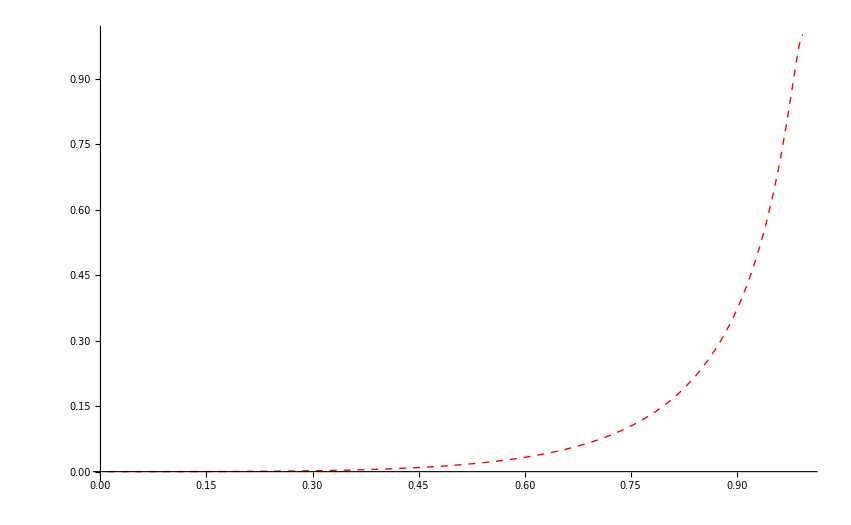

```mathematica
Plot[μ[y1]/.s2[[1]],{y1,0.01,1-10^-10},PlotRange->All,PlotStyle->{Dashed,Red}]
```

```mathematica
DSolve[i''[t]+k i[t]==0,i[t],t]//FullSimplify
```

{{i[t]→C[1] Cos[√k t]+C[2] Sin[√k t]}}

```mathematica
DSolve[{u1'[t]==-i[t]/C1,u2'[t]==-i[t]/C2,u1[t]+u2[t]==L i'[t],u1[0]==0},{u1[t],u2[t],i[t]},t]//FullSimplify
```

{{i[t]→C[1] Cosh[((C1+C2) t)/(√(-C1 C2 (C1+C2) L))]-(C1 C2 C[3] Sinh[((C1+C2) t)/(√(-C1 C2 (C1+C2) L))])/(√(-C1 C2 (C1+C2) L)),u1[t]→(-C1 C2 C[3]+C1 C2 C[3] Cosh[((C1+C2) t)/(√(-C1 C2 (C1+C2) L))]-√(-C1 C2 (C1+C2) L) C[1] Sinh[((C1+C2) t)/(√(-C1 C2 (C1+C2) L))])/(C1 (C1+C2)),u2[t]→(C2^2 C[3]+C1 C2 C[3] Cosh[((C1+C2) t)/(√(-C1 C2 (C1+C2) L))]-√(-C1 C2 (C1+C2) L) C[1] Sinh[((C1+C2) t)/(√(-C1 C2 (C1+C2) L))])/(C2 (C1+C2))}}